```mathematica
Clear["Global`*"]
<<NumericalCalculus`

(*Einstein-Dirac system of eqs with non-zero cosmological constant*)
eqns = {Sqrt[A[r]]a'[r] - a[r]*n/(2r) +b[r]*(o*T[r]+m)== 0,
Sqrt[A[r]]b'[r] - a[r]*(o*T[r]-m)+b[r]*n/(2r) == 0,
r*A'[r] -1 + A[r] + Λ*r^2 + 8*n*Pi*o*T[r]^2*(a[r]^2+b[r]^2)== 0,
2r*A[r]*T'[r]/T[r] - A[r] + 1- Λ*r^2 + 8*n*Pi*o*T[r]^2*(a[r]^2+b[r]^2) -  8*n^2*Pi*T[r]*a[r]*b[r]/r - 8*n*Pi*m*T[r]*(a[r]^2-b[r]^2)== 0 };

(* small r expansions of the fields to determine initial conditions*)
at[r_] := a1*r^(n/2);
bt[r_] := 1/(n+1)*(o*T0 - m)*a1*r^(n/2+1);
At[r_] := 1  - 8*Pi*o*T0^2*a1^2*n/(n+1)r^n -(Λ/3)r^2;
Tt[r_] := T0+T0*Sum[(Λ/3)^k *((2k-1)!!)/((2k)!!)r^(2k),{k,1,n/2}]- 4*Pi*T0^2*a1^2/(n+1)*(2*T0*o-m)*r^n 

(*initial conditions: taylor expansions of Λ fields evaluated at r=10^-5*)
v = 10^(-5);
at0 = at[v];
bt0 = bt[v];
At0 = At[v];
Tt0 = Tt[v];

(*set parameters as FSY*)
n=2;
T0 = 1;
a1 = 0.02;
m = 1;
```

```mathematica
(* numerically solve equations with initial conditions given by taylor expansions evaluated at r= v = 10^-5 *)



(*decide value of Λ, if negative Λ is large the fermions converge reall slowly so we need to solve for very large radius*)
Λ=-0.08;
If[Abs[Λ]≤ 0.01,rt=100,rt=10000];


(*BINARY SEARCH ALGORITHM*)
ωnow=5.07050216; 
ωstep=0.01;
ωstepthresh=SetPrecision [0.000000000000001,15];
ωtries={};

(*We tune ω to shoot for convergence of the fermion fields at large r
If the solver finds a node in α, ωnow is too large; if it finds it in β, then ωnow is too small*)

(* First decide whether we need to increase or decrease ω from where it is. *)
sol3=NDSolve[{{eqns,A[v]==At0, T[v]== Tt0,a[v]== at0,b[v]== bt0}/.o-> ωnow, WhenEvent[a[r]==0,{nodefound=1,"StopIntegration"}], WhenEvent[b[r]==0, {nodefound=0,"StopIntegration"}]},{A,T,a,b},{r, v, rt}];
Plot[{a[r],b[r]}/.sol3,{r,v,rt},PlotRange->{All,{-0.01,0.07}}];
AppendTo[ωtries,ωnow];
firstnodefound=nodefound;
If[firstnodefound==1,dirn=-1,dirn=1];

(* Now sweep in that direction until nodefound changes. *)
While[nodefound==firstnodefound,
ωnow+=dirn*ωstep;
sol3=NDSolve[{{eqns,A[v]==At0, T[v]== Tt0,a[v]== at0,b[v]== bt0}/.o->ωnow, WhenEvent[a[r]==0, {nodefound=1,"StopIntegration"}], WhenEvent[b[r]==0, {nodefound=0,"StopIntegration"}]},{A,T,a,b},{r, v, rt}];
 AppendTo[ωtries,ωnow]];

(* Now keep halving the step and moving in the requisite direction. *)
dirn=-dirn;
While[ωstep≥ωstepthresh,
ωstep=ωstep/2;
ωnow+=dirn*ωstep;
sol3=NDSolve[{{eqns,A[v]==At0, T[v]== Tt0,a[v]== at0,b[v]== bt0}/.o->ωnow, WhenEvent[a[r]==0, {nodefound=1,"StopIntegration"}], WhenEvent[b[r]==0, {nodefound=0,"StopIntegration"}]},{A,T,a,b},{r, v, rt}];
AppendTo[ωtries,ωnow];
If[nodefound==1,dirn=-1,dirn=1]];
ωtries;


(*solve with determined ωnow that makes the fields converge until large radius*)
sol4=NDSolve[{{eqns,A[v]==At0, T[v]== Tt0,a[v]== at0,b[v]== bt0}/.o->ωnow},{A,T,a,b},{r, v, rt}];
```

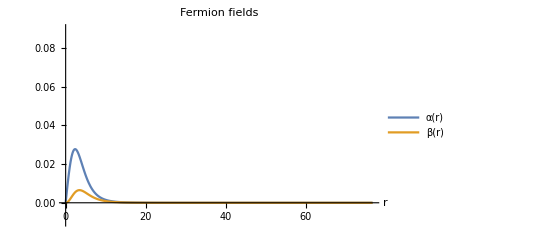

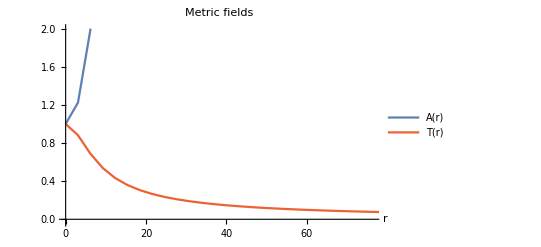

```mathematica
Plot[{a[r]/.sol4,b[r]/.sol4},{r,0,76.6737456535762},PlotRange->{{0,76.6737456535762},{-0.01,0.09}},PlotLabel->Row[Style[#,17]&/@{"Fermion fields"}],PlotLegends->Placed[LineLegend[Style[#,#,#,16]&/@{"α(r)","β(r)"}],{0.15,0.85}],AxesLabel->{Style["r",15]},TicksStyle->Directive[FontSize->14],ImageSize->{Automatic,280},Frame->Automatic]


Plot[{A[r]/.sol4,T[r]/.sol4},{r,0,rt},PlotRange-> {{0,76.36},{-0.03,2}}, 
PlotLabel->Row[Style[#,17]&/@{"Metric fields"}],TicksStyle->Directive[FontSize->14],
PlotLegends->Placed[LineLegend[Style[#,#,#,16]&/@{"A(r)","T(r)"}],{0.15,0.85}],AxesLabel->{Style["r",15]},PlotStyle->{{Dashing[{}],ColorData[97,1]},{Dashing[{}],ColorData[97,4]}},ImageSize->{Automatic,280}]
```

```mathematica
(*set up parameters for constructing the unscaled solutions that will be needed to calculate the rescalings that will give the scaled physical solutions*)
init=30;
k = Λ/3;
cutoff = 40;
cutoff2 = 50;
line1=Line[{{0,1},{rt,1}}];
lineStyle={Dashed};

Afu  = A-> sol4[[1,1,2]];
Tfu  = T-> sol4[[1,2,2]];
afu  = a-> sol4[[1,3,2]];
bfu  = b-> sol4[[1,4,2]];


(*depending on how large is, we construct solutions in different ways since if it's very negative (Λ ≤ -0.1) then we don't need to worry about the solutions diverging at large r, usually  r ~ 80 due to finite precision of the numerical solver

generate data to fit for for the Schwarzchild metric which the metric fields tend to at large r

define piecewise functions for α,β so that they are cut before the numerical solution starts to diverge*)

If[Abs[Λ]≤ 0.1, 
{Alist = Table[{i,{A[i]/.sol4}[[1,1]]},{i,init,cutoff,0.01}],
Tlist = Table[{i,{T[i]/.sol4}[[1,1]]},{i,init,cutoff,0.01}],
ak[t_]:=Piecewise[{{at[t]/.o->ωnow,0≤ t≤ v},{a[t]/.afu,v≤t≤cutoff2},{0t,cutoff<t≤Infinity}}],
bk[t_]:=Piecewise[{{bt[t]/.o->ωnow,0≤ t≤ v},{b[t]/.bfu,v≤t≤cutoff2},{0t,cutoff<t≤Infinity}}]},
{Alist = Table[{i,{A[i]/.sol4}[[1,1]]},{i,init,cutoff,0.01}],
Tlist = Table[{i,{T[i]/.sol4}[[1,1]]},{i,init,cutoff,0.01}],
ak[t_]:=Piecewise[{{at[t]/.o->ωnow,0≤ t≤ v},{a[t]/.afu,v≤t≤rt},{0t,rt<t≤Infinity}}],
bk[t_]:=Piecewise[{{bt[t]/.o->ωnow,0≤ t≤ v},{b[t]/.bfu,v≤t≤rt},{0t,rt<t≤Infinity}}]}];


(*fit general form of Schwarzchild metric of A,T to unscaled solutions*)
modelTu =tinfu / Sqrt[1 - 2Mu/r - k*r^2];
fitTu = FindFit[Tlist,modelTu,{Mu, tinfu},r];
modelTfu=Function[{r},Evaluate[modelTu/. fitTu]];

modelAu = 1 - 2Mu/r - k*r^2;
fitAu  = FindFit[Alist,modelAu,{ Mu},r];
modelAfu=Function[{r},Evaluate[modelAu/. fitAu]];
Limit[modelAfu[r],r-> Infinity];

(*define piecewise functions for A,T stitching the solutions to the Schwarzchild metric*)
Tk[t_]:=Piecewise[{{Tt[t]/.o-> ωnow,0≤ t≤ v},{T[t]/.Tfu,v≤t≤cutoff},{modelTfu[t],cutoff<t≤Infinity}}];
Ak[t_]:=Piecewise[{{At[t]/.o-> ωnow,0≤ t≤ v},{A[t]/.Afu,v≤t≤cutoff},{modelAfu[t],cutoff<t≤Infinity}}];

(*compute rescalings*)
tinfus =Limit[Sqrt[modelAfu[r]]*modelTfu[r],r-> Infinity];
integrand[x_]:= 4*Pi*Tk[x]/Sqrt[Ak[x]]*(ak[x]^2 + bk[x]^2);
l=Re[Sqrt[NIntegrate[integrand[r],{r, v,10000}]]];

(*Define scaled functions*)
Td[r_]:=Tk[l*r]/tinfus
Ad[r_]:=Ak[l*r]
ad[r_]:= Sqrt[tinfus/l]ak[l*r]
bd[r_]:= Sqrt[tinfus/l]bk[l*r]

(*compute scaled physical quantities*)
Λscal = l^2*Λ;
mscal = l*m;
ωscal = l*tinfus*ωnow;
evanes = 1/Sqrt[mscal^2 - ωscal^2];



(*fit general form of Schwarzchild metric of A,T to SCALED solutions*)
Alistscaled = Table[{i,Ad[i]},{i,init,100,1}];
Tlistscaled = Table[{i,Td[i]},{i,init,100,1}];

modelTs = Tinf/ Sqrt[1 - 2Ms/r - (Λscal/3)*r^2];
fitTs = FindFit[Tlistscaled,modelTs,{Ms,Tinf},r];
modelTfs=Function[{r},Evaluate[modelTs/. fitTs]];

modelAs = (1 - 2Ms/r - Λscal/3*r^2);
fitAs  = FindFit[Alistscaled,modelAs,{Ms},r];
modelAfs=Function[{r},Evaluate[modelAs/. fitAs]];
```

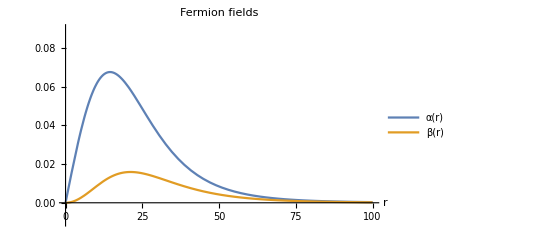

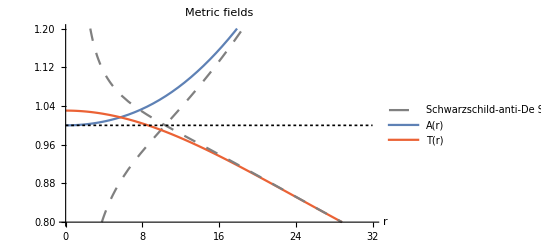

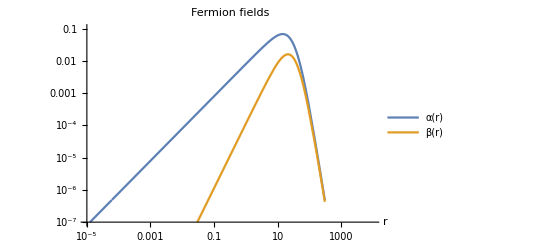

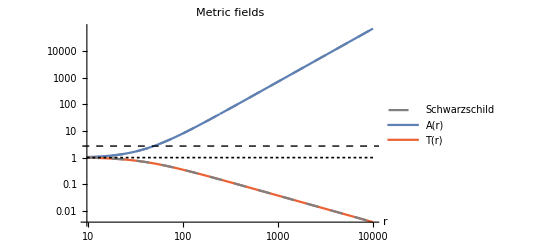

```mathematica
(*plot scaled solutions*)
Plot[{ad[x],bd[x]},{x,0,100},PlotRange->{All,{-0.01,0.09}},PlotLegends->Placed[{"α(r)","β(r)"},{0.9,0.9}],PlotLabel->Row[Style[#,17]&/@{"Fermion fields"}],BaseStyle->{FontSize->15,FontFamily->"Helvetica"},AxesLabel->{Style["r",15]},TicksStyle->Directive[FontSize->14],ImageSize->{Automatic,280}]

Plot[{modelAfs[x],Ad[x],Td[x], modelTfs[x],1},{x,0,32},PlotRange-> {All,{0.8,1.2}}, 
PlotLabel->Row[Style[#,17]&/@{"Metric fields"}],AxesLabel->{Style["r",15]},TicksStyle->Directive[FontSize->14],
PlotLegends->Placed[LineLegend[Style[#,#,#,16]&/@{"Schwarzschild-anti-De Sitter","A(r)","T(r)"}],Below],PlotStyle->{{Dashing[Medium],Gray},{Dashing[{}],ColorData[97,1]},{Dashing[{}],ColorData[97,4]},{Dashing[Medium],Gray},{Dashing[Tiny],Black,Thickness[0.003]}},ImageSize->{Automatic,280}]

LogLogPlot[{ad[x],bd[x]},{x,10^(-5),rt},PlotRange->{{10^(-5),rt},{10^(-7),0.1}},PlotLegends->Placed[{"α(r)","β(r)"},{0.2,0.9}],PlotLabel->Row[Style[#,17]&/@{"Fermion fields"}],BaseStyle->{FontSize->15,FontFamily->"Helvetica"},AxesLabel->{Style["r",15]},TicksStyle->Directive[FontSize->14],ImageSize->{Automatic,280}]


LogLogPlot[{modelAfs[x],Ad[x],Td[x], modelTfs[x],1},{x,0,rt},
PlotLabel->Row[Style[#,17]&/@{"Metric fields"}],AxesLabel->{Style["r",15]},TicksStyle->Directive[FontSize->14],
PlotLegends->Placed[LineLegend[Style[#,#,#,16]&/@{"Schwarzschild","A(r)","T(r)"}],Below],PlotStyle->{{Dashing[Medium],Gray},{Dashing[{}],,ColorData[97,1]},{Dashing[{}],ColorData[97,4]},{Dashing[Medium],Gray},{Dashing[Tiny],Black,Thickness[0.003]}},Epilog->{Directive[lineStyle],{line1}},ImageSize->{Automatic,280}]


ParametricPlot[{ad[x],bd[x]},{x,0,100},PlotLabel->"α vs β"];
```

```mathematica
(*expected behaviour of A,T at infinity*)
NLimit[Sqrt[Ad[r]]*Td[r],r-> Infinity];

(*normalisation integral*)
normintegrand[x_]:=4*Pi*Td[x]/Sqrt[Ad[x]]*(ad[x]^2 + bd[x]^2);
Plot[normintegrand[x],{x,0,300},PlotRange->All,PlotLabel->"Normalisation Integrand"];
intus[r_]:=NIntegrate[normintegrand[x],{x,0,r}];
(*Plot[{intus[r],1},{r,0,rt},PlotRange->{All,{0.98,1}},PlotStyle->{{Dashing[{}]},{Dashing[Tiny],Black,Thickness[0.003]}},PlotLabel->Row[Style[#,17]&/@{"Normalisation integral"}],BaseStyle->{FontSize->15,FontFamily->"Helvetica"},AxesLabel->{Style["r",15],Style["I(r)",15]},TicksStyle->Directive[FontSize->14],ImageSize->{Automatic,280}]*)
```

```mathematica
(*define and plot energy density and pressures from the soliton that we have solved for*)
bdprime[r_]=D[bd[r],r];
adprime[r_]=D[bd[r],r];

ρ[r_]:=n ωscal Td[r]^2/r^2*(ad[r]^2+bd[r]^2)
Pr[r_]:=n Td[r]Sqrt[Ad[r]]/r^2 (ad[r]bdprime[r]-bd[r]adprime[r])
Pϕ[r_]:= n Td[r]ad[r]bd[r]/(2r^3)

Plot[ρ[r],{r,0,rt},PlotRange->All,PlotLabel->"ρ from central solution"];
Plot[Pr[r],{r,0,rt},PlotRange->{{0,30},All},PlotLabel->"P_r from central solution"];
Plot[Pϕ[r],{r,0,rt},PlotRange->{{0,30},All},PlotLabel->"P_ϕ from central solution"];

Prlist = Table[{i,Pr[i]},{i,v,rt,1}];
ρlist = Table[{i,ρ[i]},{i,v,rt,1}];
```

```mathematica
(*DEFINE NEIGHBOURING BALLS AND FILL 3D SPACE WITH HEXAGONAL CLOSE PACKING ARRANGEMENT*)


(*define distance of the nuclei of the surrounding balls from the origin, d=2R *)
d=40;
(*vertical distance between equivalent lattice points of the HCP lattice*)
hd = 2*Sqrt[2/3]d; 
(*rmax determines how much far away from the origin the nuclei are to be included.
this effectively determines how many nearest neighbours are being computed to generate the matter background*)
rmax=40;
rsp = d/2;


(*generate points that are the nuclei of the first neighbouring balls*)
(*point in C plane*)
upoint= {0,d*Sqrt[3]/3,hd/2};
(*generate points for H,C planes*)
genHlist = Flatten[Table[{d*Cos[x], d*Sin[x], n*hd}, {x, 0, 2 Pi - Pi/3, Pi/3},{n,-3,3,1}],1];
(*important that you have n runs from -odd to odd number in gen C list *)
genClist = Flatten[Table[{upoint[[1]]+d*Cos[x],upoint[[2]]+ d*Sin[x], n*hd/2},{x, 0, 2 Pi - Pi/3, Pi/3},{n,-5,5,2}],1];
genlist = Union[genHlist,genClist];




(*can do different plots of the balls in 3D space*)

(*display spheres for genlist + a sphere at the origin*)
(*sphereHtable = Table[Sphere[{genHlist[[i,1]],genHlist[[i,2]],genHlist[[i,3]]},rsp],{i,1,Length[genHlist]}];
sphereCtable = Table[Sphere[{genClist[[i,1]],genClist[[i,2]],genClist[[i,3]]},rsp],{i,1,Length[genClist]}];
Graphics3D[{Blue,sphereHtable,Sphere[{0,0,hd},rsp],Sphere[{0,0,-hd},rsp],Sphere[{0,0,0},rsp],Red,sphereCtable,Sphere[{0,d*Sqrt[3]/3,-hd/2},rsp],Sphere[upoint,rsp]} ];*)

(*(*plot H,C layers*)
Hlist={};
Clist={};
Do[AppendTo[Hlist,Table[{genHlist[[i,1]]+d*Cos[x],genHlist[[i,2]]+ d*Sin[x], genHlist[[i,3]]}, {x, 0, 2 Pi - Pi/3, Pi/3}]],
{i,Length[genHlist]}]
ballH = Union[Flatten[Hlist,1]];
Do[AppendTo[Clist,Table[{genClist[[i,1]]+d*Cos[x],genClist[[i,2]]+ d*Sin[x], genClist[[i,3]]}, {x, 0, 2 Pi - Pi/3, Pi/3}]],
{i,Length[genClist]}]
ballC = Union[Flatten[Clist,1]];
sphereH2table = Table[Sphere[{ballH[[i,1]],ballH[[i,2]],ballH[[i,3]]},rsp],{i,1,Length[ballH]}];
sphereC2table = Table[Sphere[{ballC[[i,1]],ballC[[i,2]],ballC[[i,3]]},rsp],{i,1,Length[ballC]}];
Graphics3D[{Red,sphereH2table,Sphere[{0,0,0},rsp],Blue,sphereC2table}];*)




(*from the nearest neighbours we generate more points in the planes of the lattice*)
first= {};
second= {};
third = {};
fourth={};
ballisti={};

Do[AppendTo[first,Table[{genlist[[i,1]]+d*Cos[x],genlist[[i,2]]+ d*Sin[x], genlist[[i,3]]}, {x, 0, 2 Pi - Pi/3, Pi/3}]],
{i,Length[genlist]}]
ball1 = Union[Flatten[first,1]];

Do[AppendTo[second,Table[{ball1[[i,1]]+d*Cos[x],ball1[[i,2]]+ d*Sin[x], ball1[[i,3]]}, {x, 0, 2 Pi - Pi/3, Pi/3}]],{i,Length[ball1]}]
ball2 = Union[Flatten[second,1]];

Do[AppendTo[third,Table[{ball2[[i,1]]+d*Cos[x],ball2[[i,2]]+ d*Sin[x], ball2[[i,3]]}, {x, 0, 2 Pi - Pi/3, Pi/3}]],{i,Length[ball2]}]
ball3 = Union[Flatten[third,1]];

Do[AppendTo[fourth,Table[{ball3[[i,1]]+d*Cos[x],ball3[[i,2]]+ d*Sin[x], ball3[[i,3]]}, {x, 0, 2 Pi - Pi/3, Pi/3}]],{i,Length[ball3]}]
ball4 = Union[Flatten[fourth,1]];

Do[AppendTo[ballisti,Table[{ball4[[i,1]]+d*Cos[x],ball4[[i,2]]+ d*Sin[x], ball4[[i,3]]}, {x, 0, 2 Pi - Pi/3, Pi/3}]],{i,Length[ball4]}]
(*take away ball at the origin and remove doubles*)
ballist = Complement[Union[Flatten[ballisti,1]],{{0,0,0}}];
ListPointPlot3D[ballisti,PlotRange->All];




(*take away balls more far away than rmax*)
count=0;
table2 = Table[{0,0,0},{i,1,Length[ballist]}];
For[i=1,i≤ Length[ballist],i++,If[(ballist[[i,1]]^2+ballist[[i,2]]^2+ballist[[i,3]]^2)≤  rmax^2,count++;table2[[count]]=ballist[[i]]]]
qtable = Table[{0,0,0},{i,1,count}];
For[i=1,i≤ count,i++,qtable[[i]]=table2[[i]]]
nballs = Length[qtable];
ListPointPlot3D[qtable];




(*show the balls that you are taking into account to model your matter background*)
spheretable2 = Table[Sphere[{qtable[[i,1]],qtable[[i,2]],qtable[[i,3]]},d/2],{i,1,Length[qtable]}];
Graphics3D[{spheretable2},PlotLabel-> {nballs," Balls of R = ",d/2," at r≤",rmax," from the centre"}]
```

-Graphics3D-

```mathematica
(*define functions that sum up the contributions from the solutions centred at the neighbouring balls for each fermion fields, metric fields, energy density and pressure*)  

acombo[x_,y_,z_]:=Sum[ad[
Sqrt[(x-qtable[[i,1]])^2+(y-qtable[[i,2]])^2 + (z-qtable[[i,3]])^2]], 
{i, Length[qtable]}]
bcombo[x_,y_,z_]:=Sum[bd[
Sqrt[(x-qtable[[i,1]])^2+(y-qtable[[i,2]])^2 + (z-qtable[[i,3]])^2]], 
{i, Length[qtable]}]
Acombo[x_,y_,z_]:=Sum[Ad[
Sqrt[(x-qtable[[i,1]])^2+(y-qtable[[i,2]])^2 + (z-qtable[[i,3]])^2]], 
{i, Length[qtable]}]
Tcombo[x_,y_,z_]:=Sum[Td[
Sqrt[(x-qtable[[i,1]])^2+(y-qtable[[i,2]])^2 + (z-qtable[[i,3]])^2]], 
{i, Length[qtable]}]

rhocombo[x_,y_,z_]:=Sum[2*ωscal/((x-qtable[[i,1]])^2+(y-qtable[[i,2]])^2 + (z-qtable[[i,3]])^2) Td[
Sqrt[(x-qtable[[i,1]])^2+(y-qtable[[i,2]])^2 + (z-qtable[[i,3]])^2]
]^2*(ad[
Sqrt[(x-qtable[[i,1]])^2+(y-qtable[[i,2]])^2 + (z-qtable[[i,3]])^2]
]^2 + bd[
Sqrt[(x-qtable[[i,1]])^2+(y-qtable[[i,2]])^2 + (z-qtable[[i,3]])^2]
]^2), 
{i, Length[qtable]}]


Prtot[x_,y_,z_]:= Sum[Pr[
Sqrt[(x-qtable[[i,1]])^2+(y-qtable[[i,2]])^2 + (z-qtable[[i,3]])^2]],
{i, Length[qtable]}]
(*P_ϕ = P_θ*)
Pϕtot[x_,y_,z_]:= Sum[Pϕ[
Sqrt[(x-qtable[[i,1]])^2+(y-qtable[[i,2]])^2 + (z-qtable[[i,3]])^2]],
{i, Length[qtable]}]

(*average the pressure components at each point in order to achieve isotropy of the matter background*)
Pcombo[x_,y_,z_]:=(Prtot[x,y,z]+2*Pϕtot[x,y,z])/3
```

```mathematica
(*visualise rhocombo, Pcombo in equatorial plane, 3 fold symmetry expected from geomtry of th HCP packing*)
line4 = Line[{{Pi/6,0},{Pi/6,1}}];
line5 = Line[{{5Pi/6,0},{5/6Pi,1}}];
line6 = Line[{{3Pi/2,0},{3Pi/2,1}}];

Plot[rhocombo[10Cos[ϕ],10Sin[ϕ],0],{ϕ,Pi/6,2Pi+Pi/6},PlotRange->All,Epilog->{ line4,line5,line6}];
Plot[Pcombo[10Cos[ϕ],10Sin[ϕ],0],{ϕ,Pi/6,2Pi+Pi/6},PlotRange->All];
```

```mathematica
(*Monte carlo method to compute averages of the energy density and pressure over the solid angle at different radii, so that we can have pressure and energy density only dependent on the radial coordinate*)
(*400 points is enough to generate results with relative uncertainty of order 0.001*)

ltot = 400;
listϕ = RandomReal[{0,2Pi},Sqrt[ltot]];
listcosθ = RandomReal[{-1,1},Sqrt[ltot]];

rr = rmax+80;
radii = Table[i, {i, 0.0001,rr,1 }];

list3Drho = {};
interdatrho= {};
uncrholist = {};
list3DP = {};
interdatP= {};
uncPlist = {};


(*energy density*)
Do[
Do[AppendTo[list3Drho,rhocombo[r*Cos[i]*Sqrt[1-j^2],r*Sin[i]*Sqrt[1-j^2],r*j]],{i,listϕ},{j,listcosθ}];  
AppendTo[interdatrho,{r,Total[list3Drho]/ltot}];
AppendTo[uncrholist,{r,1/Sqrt[ltot] Sqrt[(1/ltot) Sum[(list3Drho[[i]]-Total[list3Drho]/ltot)^2,{i,1,ltot}]]}];
list3Drho = {},
{r,radii}]

(*average pressure*)
Do[
Do[AppendTo[list3DP,Pcombo[r*Cos[i]*Sqrt[1-j^2],r*Sin[i]*Sqrt[1-j^2],r*j]],{i,listϕ},{j,listcosθ}];  
AppendTo[interdatP,{r,Total[list3DP]/ltot}];
AppendTo[uncPlist,{r,1/Sqrt[ltot] Sqrt[(1/ltot) Sum[(list3DP[[i]]-Total[list3DP]/ltot)^2,{i,1,ltot}]]}];
list3DP = {},
{r,radii}]
```

```mathematica
(*interpolate the lists for the average of energy density and pressure at different radii*)
avgrho = Interpolation[interdatrho];
avgP = Interpolation[interdatP];


(*generate lists of lists for relative uncertainty*)
reluncrholist = Table[{interdatrho[[i,1]],uncrholist[[i,2]]/Abs[interdatrho[[i,2]]]},{i,1,Length[interdatrho]}];
reluncPlist = Table[{interdatP[[i,1]],uncPlist[[i,2]]/Abs[interdatP[[i,2]]]},{i,1,Length[interdatP]}];

reluncrho = Interpolation[reluncrholist];
reluncP = Interpolation[reluncPlist];
```

```mathematica
(*plot the averages of energy density and pressure that make up the matter background, also plot equation of state*)
Plot[avgrho[x],{x,0,rr},PlotRange->All, PlotLabel->Row@{"Angle-average for ρ for ",nballs," balls of R = ",d/2," present for r ≤ ",rmax," Λ=",Λ}];

Plot[avgP[x],{x,0,rr},PlotRange->All, PlotLabel->Row@{"Angle-average for average P for ",nballs," balls of R = ",d/2," present for r ≤ ",rmax,"Λ=",Λ}];

Plot[avgP[x]/avgrho[x],{x,0,rr},PlotRange->All,PlotLabel->Row@{"Eq. of state P/ρ for ",nballs," balls of R = ",d/2," present for r ≤ ",rmax,"Λ=",Λ}];

(*plot relative uncertainties, note that P might have a spike because the radial pressure crosses zero*)
Plot[reluncrho[x],{x,0,rr},PlotRange->All,PlotLabel->Row@{"ρ relative uncertainty for ",ltot," points for balls of R = ",d/2}];

Plot[reluncP[x],{x,0,rr},PlotRange->All,PlotLabel->Row@{"P relative uncertainty for ",ltot," points for balls of R = ",d/2}];
```

```mathematica
(*RESOLVE FOR CENTRAL SYSTEM EMBEDDED IN MATTER BACKGROUND*)




(*the ED system of equations is now updated, the stress energy tensor accounts for the background energy density and pressure from the surrounding balls*)

rt=100;
eqnsr = {Sqrt[A[r]]a'[r] - a[r]*n/(2r) +b[r]*(o*T[r]+m)== 0,
Sqrt[A[r]]b'[r] - a[r]*(o*T[r]-m)+b[r]*n/(2r) == 0,
r*A'[r] -1 + A[r] + Λ*r^2 + 8*n*Pi*o*T[r]^2*(a[r]^2+b[r]^2) + 8 Pi avgrho[r]r^2== 0,
2r*A[r]*T'[r]/T[r] - A[r] + 1- Λ*r^2 + 8*n*Pi*o*T[r]^2*(a[r]^2+b[r]^2) -  8*n^2*Pi*T[r]*a[r]*b[r]/r - 8*n*Pi*m*T[r]*(a[r]^2-b[r]^2)+8Pi avgP[r]r^2== 0 };

inits1 = {A[v]==At0, T[v]== Tt0,a[v]== at0,b[v]== bt0};


(*repeat procedure to shoot for convergence of the fermion fields at large r*)

ωtries={};
ωnow = 1.076; 
ωstep=0.01;
method = "Automatic";(*AccuracyGoal->40,PrecisionGoal->40,WorkingPrecision->40*)

(* First decide whether we need to increase or decrease ω from where it is. *)
sol3r=NDSolve[{{eqnsr,inits1}/.o-> ωnow, WhenEvent[a[r]==0,{nodefound=1,"StopIntegration"}], WhenEvent[b[r]==0, {nodefound=0,"StopIntegration"}]},{A,T,a,b},{r, v, rt},Method->method];
AppendTo[ωtries,ωnow];
firstnodefound=nodefound;
If[firstnodefound==1,dirn=-1,dirn=1];

(* Now sweep in that direction until nodefound changes. *)
While[nodefound==firstnodefound,
ωnow+=dirn*ωstep;
sol3r=NDSolve[{{eqnsr,inits1}/.o->ωnow, WhenEvent[a[r]==0, {nodefound=1,"StopIntegration"}], WhenEvent[b[r]==0, {nodefound=0,"StopIntegration"}]},{A,T,a,b},{r, v, rt},Method->method];
 AppendTo[ωtries,ωnow]];
ωtries;

(* Now keep halving the step and moving in the requisite direction. *)
dirn=-dirn;
While[ωstep≥ωstepthresh,
ωstep=ωstep/2;
ωnow+=dirn*ωstep;
sol3r=NDSolve[{{eqnsr,A[v]==At0, T[v]== Tt0,a[v]== at0,b[v]== bt0}/.o->ωnow, WhenEvent[a[r]==0, {nodefound=1,"StopIntegration"}], WhenEvent[b[r]==0, {nodefound=0,"StopIntegration"}]},{A,T,a,b},{r, v, rt},Method->method];
AppendTo[ωtries,ωnow];
If[nodefound==1,dirn=-1,dirn=1]];
ωtries;>
ωnow;

sol4r=NDSolve[{{eqnsr,inits1}/.o->ωnow},{A,T,a,b},{r, v, rt},Method->method];
```

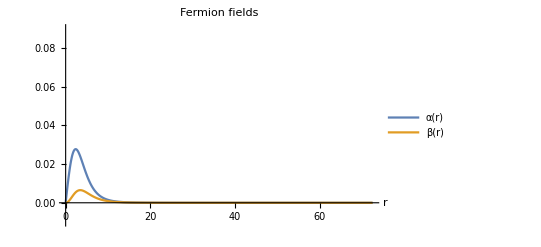

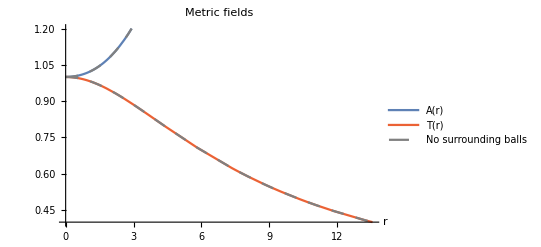

```mathematica
(*plot solution*)

(*the numerical solver terminates the solutions in presence of the energy density and matter background from the neighbourin balls very early, especially for the metric fields, before they can recover a form that can be fitted with analytical solutions.

we have tried to increase WorkingPrecision, AccuracyGoal, MachinePrecision as well as different solvers such as StiffnessSwitching, ExplicitRungeKutta, LSODA and others but unfortunately none could evaluate until a large enough radius

 this prevents the construction of the unscaled solutions, and consequently the computation of the rescalings and construction of the scaled physical solutions
*)

Plot[{a[r]/.sol4r,b[r]/.sol4r},{r,v,72.43},PlotRange->{All,{-0.01,0.09}},PlotLegends->Placed[LineLegend[Style[#,#,#,16]&/@{"α(r)","β(r)"}],Below],PlotLabel->Row[Style[#,17]&/@{"Fermion fields"}],AxesLabel->{Style["r",15]},TicksStyle->Directive[FontSize->14],ImageSize->{Automatic,280}]

Plot[{A[r]/.sol4r,T[r]/.sol4r,A[r]/.sol4,T[r]/.sol4},{r,v,72.43},PlotRange->{{0,All},{0.4,1.2}},PlotLegends->Placed[LineLegend[Style[#,#,#,16]&/@{"A(r)","T(r)","No surrounding balls"}],Below],PlotLabel->Row[Style[#,17]&/@{"Metric fields"}],AxesLabel->{Style["r",15]},TicksStyle->Directive[FontSize->14],ImageSize->{Automatic,280},PlotStyle->{{Dashing[{}],ColorData[97,1]},{Dashing[{}],ColorData[97,4]},{Dashing[Medium],Gray},{Dashing[Medium],Gray}}]
```